```mathematica
(*Import the dUdL for GibbsBog/4_longRun_4.8_2_3_v1v2, integrate it and determine the MVT L value*)
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/thermodynamic_integration_analysis/GibbsBog/4_LONG50000_4.8_2_3_v1v2"];
dudlFiles={"T_all_vol_dUdL"}
(*Data format, col1=L, col2=vol1, col2=vol2...*)
dudlDat=Table[ReadList[dudlFiles[[i]],{Number, Number,Number,Number,Number,Number}],{i,1,1}];
```

{T_all_vol_dUdL}

```mathematica
dudlV1=Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[2]]}],11]
```

{{{0.,1.30659},{0.1,1.20401},{0.2,1.12086},{0.3,1.02628},{0.4,0.944786},{0.5,0.881883},{0.6,0.796387},{0.7,0.732104},{0.8,0.648583},{0.9,0.564847},{1.,0.499554}},{{0.,3.5151},{0.1,3.06015},{0.2,2.76378},{0.3,2.37159},{0.4,2.00772},{0.5,1.78403},{0.6,1.40765},{0.7,1.18241},{0.8,0.837762},{0.9,0.545886},{1.,0.242771}},{{0.,11.7289},{0.1,9.21876},{0.2,7.06729},{0.3,5.59193},{0.4,3.94368},{0.5,2.64249},{0.6,1.33998},{0.7,-0.113194},{0.8,-1.20071},{0.9,-2.98913},{1.,-4.24493}},{{0.,17.2962},{0.1,13.4791},{0.2,9.45208},{0.3,6.7659},{0.4,4.40979},{0.5,2.05609},{0.6,-0.389434},{0.7,-2.50651},{0.8,-4.95798},{0.9,-7.04485},{1.,-9.51967}},{{0.,26.0482},{0.1,19.075},{0.2,12.8074},{0.3,7.84285},{0.4,4.32939},{0.5,-0.123227},{0.6,-3.77368},{0.7,-7.10087},{0.8,-11.389},{0.9,-15.2243},{1.,-19.4012}},{{0.,36.6604},{0.1,23.188},{0.2,15.5019},{0.3,8.69108},{0.4,2.98479},{0.5,-3.05327},{0.6,-8.68298},{0.7,-13.4081},{0.8,-19.1642},{0.9,-25.8436},{1.,-34.1356}}}

```mathematica
dudlAll=Table[Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[1+vol]]}],11],{vol,1,5}];
```

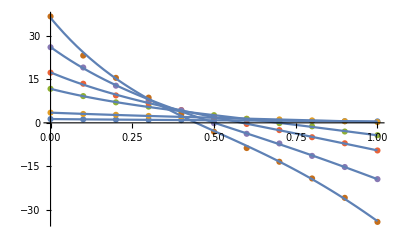

```mathematica
Show[ListPlot[dudlAll[[1]]],Plot[dudlAllFitD4[[1]],{L,0,1}]]
```

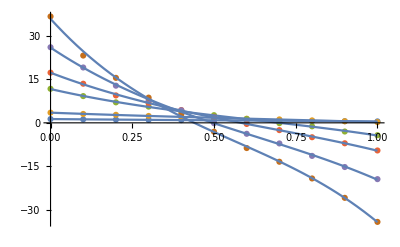

```mathematica
Show[ListPlot[dudlAll[[1]]],Plot[dudlAllFitD[[1]],{L,0,1}]]
```

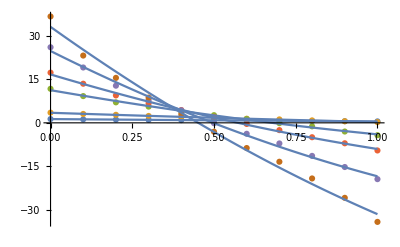

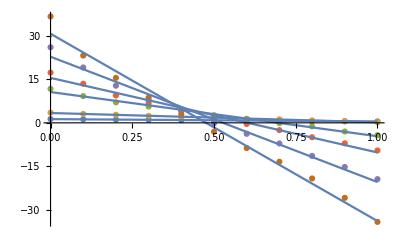

```mathematica
Show[ListPlot[dudlAll[[1]]],Plot[dudlAllFitD2[[1]],{L,0,1}]]
Show[ListPlot[dudlAll[[1]]],Plot[dudlAllFitD1[[1]],{L,0,1}]]
```

```mathematica
dudlAllFit=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,5}];
dudlAllFitD=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,5}]
dudlAllFit2=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^2,L,1},L],{temp,1,6,1}],{vol,1,5}];
dudlAllFitD2=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^2,L,1},L],{temp,1,6,1}],{vol,1,5}]
dudlAllFitD1=Table[Table[Fit[dudlAll[[vol]][[temp]],{L,1},L],{temp,1,6,1}],{vol,1,5}]
dudlAllFitD4=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^4,L^2,L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,5}]
```

{{1.30535-1.02642 L+0.437308 L^2-0.221906 L^3,3.50485-4.27332 L+1.96964 L^2-0.963436 L^3,11.653-25.7989 L+20.7372 L^2-10.9561 L^3,17.2756-43.0008 L+32.4126 L^2-16.2891 L^3,25.9369-75.0647 L+62.2042 L^2-32.6762 L^3,35.84-124.295 L+131.03 L^2-76.8077 L^3},{1.03267-1.08354 L+0.356708 L^2-0.115487 L^3,3.77489-4.66958 L+1.62043 L^2-0.534747 L^3,15.6839-29.7196 L+21.0123 L^2-9.54346 L^3,24.4055-55.6081 L+46.8534 L^2-22.6229 L^3,36.9805-97.6475 L+91.037 L^2-46.0386 L^3,51.8903-166.601 L+192.269 L^2-105.92 L^3},{0.690609-0.808532 L-0.276618 L^2+0.220768 L^3,3.96908-6.14786 L+3.77725 L^2-1.58515 L^3,18.5182-36.648 L+30.1122 L^2-13.7389 L^3,29.3969-65.6596 L+57.2451 L^2-26.409 L^3,46.893-131.207 L+144.085 L^2-74.0086 L^3,66.1153-216.055 L+265.916 L^2-142.234 L^3},{0.221515-1.30479 L+0.551101 L^2-0.223085 L^3,4.0892-6.50414 L+2.89921 L^2-0.894827 L^3,23.3059-47.0878 L+40.1645 L^2-17.403 L^3,38.9302-95.7787 L+100.83 L^2-48.8926 L^3,60.6742-171.83 L+198.218 L^2-100.727 L^3,86.1221-284.519 L+370.656 L^2-199.209 L^3},{-0.144627-1.42759 L+0.487917 L^2-0.187542 L^3,4.92294-10.3458 L+7.84525 L^2-3.18967 L^3,31.1276-70.5405 L+71.0677 L^2-32.6614 L^3,52.5759-136.874 L+152.068 L^2-72.4236 L^3,86.1588-275.739 L+362.899 L^2-188.299 L^3,126.202-466.298 L+662.531 L^2-353.201 L^3}}

{{1.29736-0.899486 L+0.104448 L^2,3.47017-3.72223 L+0.524488 L^2,11.2586-19.5321 L+4.30309 L^2,16.6891-33.6834 L+7.97889 L^2,24.7605-56.3739 L+13.19 L^2,33.0749-80.3609 L+15.8181 L^2},{1.02851-1.01748 L+0.183478 L^2,3.75564-4.3637 L+0.818312 L^2,15.3404-24.2608 L+6.69712 L^2,23.5911-42.6679 L+12.919 L^2,35.3231-71.3135 L+21.9792 L^2,48.0772-106.014 L+33.388 L^2},{0.698557-0.934811 L+0.0545341 L^2,3.91201-5.24115 L+1.39952 L^2,18.0236-28.7893 L+9.50382 L^2,28.4462-50.5536 L+17.6317 L^2,44.2287-88.8737 L+33.0718 L^2,60.9949-134.697 L+52.5644 L^2},{0.213484-1.17718 L+0.216473 L^2,4.05698-5.9923 L+1.55697 L^2,22.6794-37.1332 L+14.06 L^2,37.17-67.8121 L+27.4913 L^2,57.048-114.214 L+47.1267 L^2,78.9506-170.572 L+71.8429 L^2},{-0.151378-1.32032 L+0.206604 L^2,4.80811-8.52129 L+3.06075 L^2,29.9518-51.8581 L+22.0755 L^2,49.9686-95.4474 L+43.4325 L^2,79.38-168.032 L+80.4508 L^2,113.486-264.267 L+132.73 L^2}}

{{1.28169-0.795038 L,3.39149-3.19774 L,10.6131-15.229 L,15.4923-25.7045 L,22.782-43.184 L,30.7022-64.5428 L},{1.00099-0.834 L,3.63289-3.54539 L,14.3358-17.5636 L,21.6532-29.7488 L,32.0262-49.3343 L,43.069-72.6264 L},{0.690377-0.880277 L,3.70208-3.84162 L,16.598-19.2855 L,25.8014-32.922 L,39.268-55.8019 L,53.1102-82.1328 L},{0.181013-0.960707 L,3.82344-4.43532 L,20.5704-23.0733 L,33.0463-40.3208 L,49.979-67.0876 L,68.1742-98.7291 L},{-0.182369-1.11372 L,4.349-5.46053 L,26.6405-29.7826 L,43.4538-52.0149 L,67.3124-87.5815 L,93.5769-131.537 L}}

{{1.30754-1.10266 L+0.818536 L^2-0.831871 L^3+0.304983 L^4,3.50723-4.35594 L+2.38273 L^2-1.62438 L^3+0.330472 L^4,11.7335-28.5942 L+34.7138 L^2-33.3186 L^3+11.1812 L^4,17.3856-46.8234 L+51.5256 L^2-46.8699 L^3+15.2904 L^4,26.1259-81.6271 L+95.0163 L^2-85.1756 L^3+26.2497 L^4,36.1895-136.431 L+191.712 L^2-173.899 L^3+48.5456 L^4},{1.03464-1.15179 L+0.69797 L^2-0.661507 L^3+0.27301 L^4,3.78398-4.98543 L+3.19971 L^2-3.06159 L^3+1.26342 L^4,15.7579-32.2885 L+33.8568 L^2-30.0946 L^3+10.2756 L^4,24.5511-60.6641 L+72.1332 L^2-63.0707 L^3+20.2239 L^4,37.401-112.25 L+164.047 L^2-162.855 L^3+58.4082 L^4,52.7709-197.177 L+345.15 L^2-350.53 L^3+122.305 L^4},{0.677831-0.364825 L-2.49515 L^2+3.77042 L^3-1.77483 L^4,3.96325-5.94571 L+2.7665 L^2+0.0320501 L^3-0.808602 L^4,18.6308-40.5565 L+49.6547 L^2-45.0069 L^3+15.634 L^4,29.6802-75.4976 L+106.435 L^2-105.113 L^3+39.352 L^4,47.5458-153.873 L+257.417 L^2-255.34 L^3+90.6658 L^4,67.8731-277.091 L+571.093 L^2-630.519 L^3+244.142 L^4},{0.22636-1.47302 L+1.39228 L^2-1.56897 L^3+0.672942 L^4,4.09692-6.77237 L+4.24038 L^2-3.04069 L^3+1.07293 L^4,23.4765-53.0102 L+69.7768 L^2-64.7828 L^3+23.6899 L^4,39.3621-110.775 L+175.814 L^2-168.866 L^3+59.9868 L^4,61.7393-208.81 L+383.118 L^2-396.567 L^3+147.92 L^4,88.0825-352.588 L+710.997 L^2-743.754 L^3+272.273 L^4},{-0.139221-1.61529 L+1.42641 L^2-1.68914 L^3+0.750798 L^4,4.94318-11.0486 L+11.3594 L^2-8.81223 L^3+2.81128 L^4,31.3705-78.9753 L+113.242 L^2-100.14 L^3+33.7392 L^4,53.3951-165.319 L+294.295 L^2-299.987 L^3+113.782 L^4,87.8829-335.605 L+662.23 L^2-667.229 L^3+239.465 L^4,130.84-627.364 L+1467.86 L^2-1641.73 L^3+644.266 L^4}}

```mathematica
bound1=0;bound2=1; mvtSolver[function_]:=Solve[Evaluate@function==(Integrate[Evaluate@function,{L,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2})&&L∈Interval[{0,1}],L,Reals]//N
dudlIntegrator[function_]:=NIntegrate[function,{L,bound1,bound2}]
```

```mathematica
(*print the MVT solver L value, the mid point L=0.5 dUdL value approximation to int dUdL, and the proper integrated value*)
midValintValMVT[fun_]:={mvtSolver[fun],
fun/.L->0.5,
dudlIntegrator[fun]}
midValintValMVT[dudlAllFit[[1]][[1]]]
```

{{{L→{0.488498}}},0.873726,0.88243}

```mathematica
(*vol1,temp*)
dudlOut=Table[Table[midValintValMVT[dudlAllFit[[vol]][[temp]]],{temp,1,6}]//TableForm,{vol,1,5}];
"MVT L, midpoint intval, intval"
dudlOut//TableForm
```

MVT L, midpoint intval, intval

L→{0.488498} | 0.873726 | 0.88243
L→{0.485594} | 1.74017 | 1.78388
L→{0.473243} | 2.56833 | 2.92692
L→{0.471152} | 1.84218 | 2.50708
L→{0.470905} | -0.128944 | 0.970219
L→{0.474319} | -3.15104 | -1.83287
L→{0.481284} | 0.565644 | 0.580934
L→{0.480328} | 1.77836 | 1.84655
L→{0.465354} | 4.88428 | 5.44238
L→{0.459048} | 5.48692 | 6.56351
L→{0.456577} | 5.16118 | 6.99278
L→{0.450052} | 3.41695 | 6.19928
L→{0.495059} | 0.244785 | 0.24933
L→{0.467661} | 1.64132 | 1.75795
L→{0.45423} | 6.00491 | 6.79689
L→{0.44964} | 7.57729 | 9.04659
L→{0.438668} | 8.05981 | 10.8158
L→{0.42854} | 6.78737 | 11.1677
L→{0.480504} | -0.320988 | -0.302949
L→{0.469991} | 1.45008 | 1.57983
L→{0.443729} | 7.6278 | 8.79946
L→{0.432044} | 10.1368 | 12.4277
L→{0.426162} | 11.7226 | 15.6498
L→{0.415407} | 11.6254 | 17.6123
L→{0.484112} | -0.759887 | -0.74267
L→{0.449546} | 1.31265 | 1.56772
L→{0.428462} | 9.54163 | 11.3813
L→{0.416342} | 13.1031 | 16.7225
L→{0.396006} | 15.4766 | 22.1808
L→{0.377431} | 14.5356 | 25.5964

```mathematica
(*vol1,temp*)
dudlOut2=Table[Table[midValintValMVT[dudlAllFit2[[vol]][[temp]]],{temp,1,6}]//TableForm,{vol,1,5}];
"MVT L, midpoint intval, intval"
dudlOut2//TableForm
```

MVT L, midpoint intval, intval

L→{0.489068} | 0.873726 | 0.88243
L→{0.486362} | 1.74017 | 1.78388
L→{0.476608} | 2.56833 | 2.92692
L→{0.474337} | 1.84218 | 2.50708
L→{0.474742} | -0.128944 | 0.970219
L→{0.479678} | -3.15104 | -1.83287
L→{0.48174} | 0.565644 | 0.580934
L→{0.48085} | 1.77836 | 1.84655
L→{0.4686} | 4.88428 | 5.44238
L→{0.464362} | 5.48692 | 6.56351
L→{0.463468} | 5.16118 | 6.99278
L→{0.462342} | 3.41695 | 6.19928
L→{0.494839} | 0.244785 | 0.24933
L→{0.46997} | 1.64132 | 1.75795
L→{0.459733} | 6.00491 | 6.79689
L→{0.456389} | 7.57729 | 9.04659
L→{0.451978} | 8.05981 | 10.8158
L→{0.448373} | 6.78737 | 11.1677
L→{0.481302} | -0.320988 | -0.302949
L→{0.471041} | 1.45008 | 1.57983
L→{0.450701} | 7.6278 | 8.79946
L→{0.445228} | 10.1368 | 12.4277
L→{0.443689} | 11.7226 | 15.6498
L→{0.441823} | 11.6254 | 17.6123
L→{0.484585} | -0.759887 | -0.74267
L→{0.454453} | 1.31265 | 1.56772
L→{0.440827} | 9.54163 | 11.3813
L→{0.434048} | 13.1031 | 16.7225
L→{0.428189} | 15.4766 | 22.1808
L→{0.422043} | 14.5356 | 25.5964

```mathematica
(*vol1,temp*)
dudlOut1=Table[Table[midValintValMVT[dudlAllFitD1[[vol]][[temp]]],{temp,1,6}]//TableForm,{vol,1,5}];
"MVT L, midpoint intval, intval"
dudlOut1//TableForm
```

MVT L, midpoint intval, intval

L→{0.5} | 0.884171 | 0.884171
L→{0.5} | 1.79262 | 1.79262
L→{0.5} | 2.99864 | 2.99864
L→{0.5} | 2.64007 | 2.64007
L→{0.5} | 1.19005 | 1.19005
L→{0.5} | -1.56923 | -1.56923
L→{0.5} | 0.583992 | 0.583992
L→{0.5} | 1.86019 | 1.86019
L→{0.5} | 5.55399 | 5.55399
L→{0.5} | 6.77882 | 6.77882
L→{0.5} | 7.3591 | 7.3591
L→{0.5} | 6.75574 | 6.75574
L→{0.5} | 0.250239 | 0.250239
L→{0.5} | 1.78127 | 1.78127
L→{0.5} | 6.95529 | 6.95529
L→{0.5} | 9.34045 | 9.34045
L→{0.5} | 11.367 | 11.367
L→{0.5} | 12.0438 | 12.0438
L→{0.5} | -0.299341 | -0.299341
L→{0.5} | 1.60578 | 1.60578
L→{0.5} | 9.0338 | 9.0338
L→{0.5} | 12.8859 | 12.8859
L→{0.5} | 16.4352 | 16.4352
L→{0.5} | 18.8096 | 18.8096
L→{0.5} | -0.739227 | -0.739227
L→{0.5} | 1.61873 | 1.61873
L→{0.5} | 11.7492 | 11.7492
L→{0.5} | 17.4463 | 17.4463
L→{0.5} | 23.5217 | 23.5217
L→{0.5} | 27.8086 | 27.8086

```mathematica
(*vol1,temp*)
dudlOut4=Table[Table[midValintValMVT[dudlAllFitD4[[vol]][[temp]]],{temp,1,6}]//TableForm,{vol,1,5}];
"MVT L, midpoint intval, intval"
dudlOut4//TableForm
```

MVT L, midpoint intval, intval

L→{0.491846} | 0.875922 | 0.882085
L→{0.486495} | 1.74255 | 1.78351
L→{0.480064} | 2.64884 | 2.91425
L→{0.476541} | 1.95227 | 2.48975
L→{0.476548} | 0.0600537 | 0.940469
L→{0.482072} | -2.80152 | -1.88789
L→{0.484037} | 0.56761 | 0.580625
L→{0.483328} | 1.78746 | 1.84512
L→{0.470463} | 4.95827 | 5.43073
L→{0.465108} | 5.63253 | 6.54059
L→{0.467538} | 5.58172 | 6.92658
L→{0.467338} | 4.29754 | 6.06067
L→{0.479206} | 0.232006 | 0.251341
L→{0.465883} | 1.6355 | 1.75886
L→{0.461255} | 6.11747 | 6.77917
L→{0.46006} | 7.86062 | 9.00199
L→{0.453775} | 8.7126 | 10.713
L→{0.458645} | 8.54519 | 10.891
L→{0.486512} | -0.316143 | -0.303711
L→{0.471989} | 1.4578 | 1.57861
L→{0.452257} | 7.79837 | 8.77261
L→{0.444833} | 10.5687 | 12.3598
L→{0.44613} | 12.7876 | 15.4822
L→{0.442096} | 13.5857 | 17.3037
L→{0.489857} | -0.754481 | -0.743521
L→{0.453755} | 1.33289 | 1.56453
L→{0.437552} | 9.78455 | 11.343
L→{0.433981} | 13.9223 | 16.5935
L→{0.417638} | 17.2007 | 21.9094
L→{0.417615} | 19.1743 | 24.8662

```mathematica
vols={4.685,4.730,4.759,4.801,4.850};
```

0.488498 | 0.485594 | 0.473243 | 0.471152 | 0.470905 | 0.474319
0.481284 | 0.480328 | 0.465354 | 0.459048 | 0.456577 | 0.450052
0.495059 | 0.467661 | 0.45423 | 0.44964 | 0.438668 | 0.42854
0.480504 | 0.469991 | 0.443729 | 0.432044 | 0.426162 | 0.415407
0.484112 | 0.449546 | 0.428462 | 0.416342 | 0.396006 | 0.377431

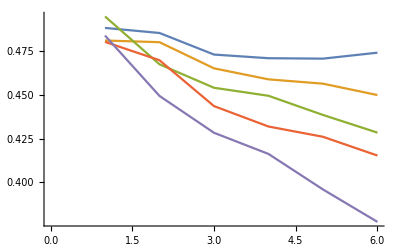

```mathematica
mvtOut=Table[Table[dudlOut[[vol]][[1]][[temp]][[1]][[1]][[1]][[2]][[1]],{temp,1,6}],{vol,1,5}];
mvtOut//TableForm
ListLinePlot[mvtOut]
```

0.489068 | 0.486362 | 0.476608 | 0.474337 | 0.474742 | 0.479678
0.48174 | 0.48085 | 0.4686 | 0.464362 | 0.463468 | 0.462342
0.494839 | 0.46997 | 0.459733 | 0.456389 | 0.451978 | 0.448373
0.481302 | 0.471041 | 0.450701 | 0.445228 | 0.443689 | 0.441823
0.484585 | 0.454453 | 0.440827 | 0.434048 | 0.428189 | 0.422043

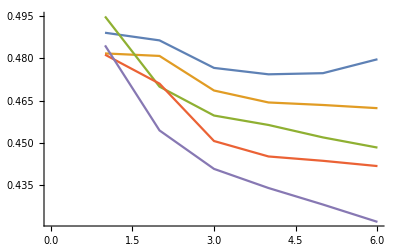

```mathematica
mvtOut2=Table[Table[dudlOut2[[vol]][[1]][[temp]][[1]][[1]][[1]][[2]][[1]],{temp,1,6}],{vol,1,5}];
mvtOut2//TableForm
ListLinePlot[mvtOut2]
```

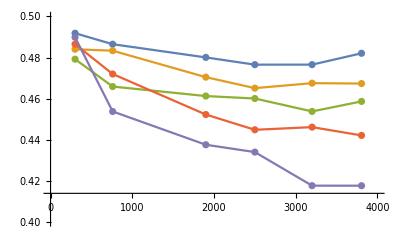

```mathematica
Show[{ListPlot[mvtOut4],ListLinePlot[mvtOut4]},PlotRange->{{0,4000},{0.4,0.5}}]
```

```mathematica
tt={300,760,1900,2500,3200,3805};
```

```mathematica
mvtOut4[[1]]
```

{{300,0.491846},{760,0.486495},{1500,0.480064},{3200,0.476541},{3805,0.476548},{{300,760,1500,3200,3805}⟦6⟧,0.482072}}

```mathematica
mvtOut4=Table[Table[{tt[[temp]],dudlOut4[[vol]][[1]][[temp]][[1]][[1]][[1]][[2]][[1]]},{temp,1,6}],{vol,1,5}];
mvtOut4//TableForm
Table[Table[dudlOut4[[vol]][[1]][[temp]][[1]][[1]][[1]][[2]][[1]],{temp,1,6}],{vol,1,5}]//TableForm
```

300
0.491846 | 760
0.486495 | 1900
0.480064 | 2500
0.476541 | 3200
0.476548 | 3805
0.482072
300
0.484037 | 760
0.483328 | 1900
0.470463 | 2500
0.465108 | 3200
0.467538 | 3805
0.467338
300
0.479206 | 760
0.465883 | 1900
0.461255 | 2500
0.46006 | 3200
0.453775 | 3805
0.458645
300
0.486512 | 760
0.471989 | 1900
0.452257 | 2500
0.444833 | 3200
0.44613 | 3805
0.442096
300
0.489857 | 760
0.453755 | 1900
0.437552 | 2500
0.433981 | 3200
0.417638 | 3805
0.417615

0.491846 | 0.486495 | 0.480064 | 0.476541 | 0.476548 | 0.482072
0.484037 | 0.483328 | 0.470463 | 0.465108 | 0.467538 | 0.467338
0.479206 | 0.465883 | 0.461255 | 0.46006 | 0.453775 | 0.458645
0.486512 | 0.471989 | 0.452257 | 0.444833 | 0.44613 | 0.442096
0.489857 | 0.453755 | 0.437552 | 0.433981 | 0.417638 | 0.417615

```mathematica
mvtOut[[1]]
```

{{{4.685,4.73,4.759,4.801,4.85},0.488498},{{4.685,4.73,4.759,4.801,4.85},0.485594},{{4.685,4.73,4.759,4.801,4.85},0.473243},{{4.685,4.73,4.759,4.801,4.85},0.471152},{{4.685,4.73,4.759,4.801,4.85},0.470905},{{4.685,4.73,4.759,4.801,4.85},0.474319}}

```mathematica
"MVT L, midpoint intval, intval"
Table[midValintValMVT[dudlAllFit[[2]][[temp]]],{temp,1,6}]//TableForm
```

MVT L, midpoint intval, intval

L→0.475865
L→0.62748-0.883604 ⅈ
L→0.62748+0.883604 ⅈ | 0.540333 | 0.557211
L→0.47199
L→1.35812-2.07033 ⅈ
L→1.35812+2.07033 ⅈ | 1.74007 | 1.83662
L→0.461402
L→1.02677-1.3834 ⅈ
L→1.02677+1.3834 ⅈ | 4.78175 | 5.40044
L→0.447247
L→0.877367-0.983107 ⅈ
L→0.877367+0.983107 ⅈ | 5.51949 | 6.93238
L→0.46644
L→0.696818-0.924858 ⅈ
L→0.696818+0.924858 ⅈ | 5.80187 | 7.26056
L→0.438019
L→0.660649-0.568194 ⅈ
L→0.660649+0.568194 ⅈ | 3.5649 | 6.70962

```mathematica
"MVT L, midpoint intval, intval"
Table[midValintValMVT[dudlAllFit[[3]][[temp]]],{temp,1,6}]//TableForm
```

MVT L, midpoint intval, intval

L→-1.23555
L→0.473307
L→1.6326 | 0.200353 | 0.228736
L→-1.54362
L→0.477697
L→1.83548 | 1.59907 | 1.68641
L→0.464381
L→0.841939-1.18309 ⅈ
L→0.841939+1.18309 ⅈ | 6.12687 | 6.74697
L→0.451758
L→0.836322-0.982588 ⅈ
L→0.836322+0.982588 ⅈ | 7.30774 | 8.75929
L→0.436474
L→0.800494-0.784058 ⅈ
L→0.800494+0.784058 ⅈ | 8.01611 | 10.9363
L→0.44167
L→0.756563-0.764146 ⅈ
L→0.756563+0.764146 ⅈ | 7.17317 | 10.9704